```mathematica
D[c0*x^b0*c1*x^b1/(c0*x^b0+c1*x^b1),x]
```

-(c0 c1 x^(b0+b1) (b0 c0 x^(-1+b0)+b1 c1 x^(-1+b1)))/((c0 x^b0+c1 x^b1)^2)+((b0+b1) c0 c1 x^(-1+b0+b1))/(c0 x^b0+c1 x^b1)

```mathematica
Solve[-(c0 c1 x^(b0+b1) (b0 c0 x^(-1+b0)+b1 c1 x^(-1+b1)))/((c0 x^b0+c1 x^b1)^2)+((b0+b1) c0 c1 x^(-1+b0+b1))/(c0 x^b0+c1 x^b1)==0,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→ⅇ^((-ⅈ π+Log[b0]-Log[b1]-Log[c0]+Log[c1])/(b0-b1))}}

```mathematica
Solve[c0*x^b0*c1*x^b1/(c0*x^b0+c1*x^b1)==0,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→0^(1/(b0+b1))}}

```mathematica
recoverydta=Table[{10^i,Recovery/.{M->10^i}},{i,1,8,.25}]
```

{{10.,1.97362×10^-6},{17.7828,1.56641×10^-6},{31.6228,1.24526×10^-6},{56.2341,9.91645×10^-7},{100.,7.91067×10^-7},{177.828,6.32193×10^-7},{316.228,5.06149×10^-7},{562.341,4.05986×10^-7},{1000.,3.26251×10^-7},{1778.28,2.62666×10^-7},{3162.28,2.11867×10^-7},{5623.41,1.71208×10^-7},{10000.,1.38603×10^-7},{17782.8,1.12407×10^-7},{31622.8,9.13205×10^-8},{56234.1,7.43136×10^-8},{100000.,6.05712×10^-8},{177828.,4.94456×10^-8},{316228.,4.04216×10^-8},{562341.,3.30887×10^-8},{1.×10^6,2.71192×10^-8},{1.77828×10^6,2.22508×10^-8},{3.16228×10^6,1.82734×10^-8},{5.62341×10^6,1.50182×10^-8},{1.×10^7,1.23493×10^-8},{1.77828×10^7,1.01569×10^-8},{3.16228×10^7,8.35242×10^-9},{5.62341×10^7,6.8635×10^-9},{1.×10^8,5.63094×10^-9}}

```mathematica
recoveryfit={E^d,e}/.FindFit[Log[recoverydta],d+e*x,{d,e},x]
```

{4.10006×10^-6,-0.361927}

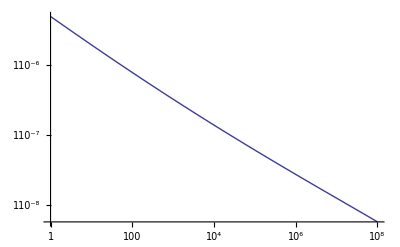

```mathematica
LogLogPlot[Recovery,{M,1,10^8}]
```

```mathematica
starvedta=Table[{10^i,Starvation/.{M->10^i}},{i,1,8,.25}]
```

{{10.,0.000118786},{17.7828,0.0000920358},{31.6228,0.000071294},{56.2341,0.000055213},{100.,0.0000427472},{177.828,0.0000330854},{316.228,0.0000255984},{562.341,0.0000197976},{1000.,0.0000153044},{1778.28,0.000011825},{3162.28,9.13125×10^-6},{5623.41,7.04651×10^-6},{10000.,5.43366×10^-6},{17782.8,4.18638×10^-6},{31622.8,3.22225×10^-6},{56234.1,2.47737×10^-6},{100000.,1.90221×10^-6},{177828.,1.45839×10^-6},{316228.,1.11616×10^-6},{562341.,8.52491×10^-7},{1.×10^6,6.49527×10^-7},{1.77828×10^6,4.93454×10^-7},{3.16228×10^6,3.73578×10^-7},{5.62341×10^6,2.8162×10^-7},{1.×10^7,2.11175×10^-7},{1.77828×10^7,1.57288×10^-7},{3.16228×10^7,1.16125×10^-7},{5.62341×10^7,8.47144×10^-8},{1.×10^8,6.07469×10^-8}}

```mathematica
starvefit={E^d,e}/.FindFit[Log[starvedta],d+e*x,{d,e},x]
```

{0.000373331,-0.463825}

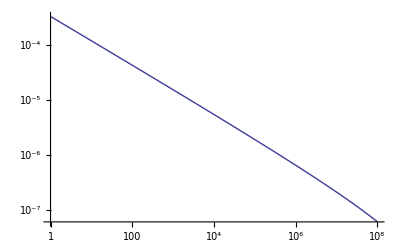

```mathematica
LogLogPlot[Starvation,{M,1,10^8}]
```

```mathematica
c0=recoveryfit[[1]]
b0=recoveryfit[[2]]

c1=starvefit[[1]]
b1=starvefit[[2]]
```

4.10006×10^-6

-0.361927

0.000373331

-0.463825

```mathematica
(-1*c1*b0/(c0*b1))^(1/(b0-b1))
```

1.23506×10^18-8.18546×10^17 ⅈ

```mathematica
ⅇ^((-ⅈ π+Log[b0]-Log[b1]-Log[c0]+Log[c1])/(b0-b1))
```

1.23506×10^18+8.18546×10^17 ⅈ

```mathematica
N[Recovery*Starvation/(Starvation+Recovery)==0,M]
```

N::precbd: Requested precision M is not a machine-sized real number between $MinPrecision and $MaxPrecision.

N[1.12704×10^-11/(√M Log[0.0127415/(1-0.987259 (1-0.0202 M^0.19)^(1/4))] (-(1.67857×10^-6)/(M^(1/4) Log[0.0127415/(1-0.987259 (1-0.0202 M^0.19)^(1/4))])-(6.71429×10^-6)/(M^(1/4) Log[1-0.0202 M^0.19])) Log[1-0.0202 M^0.19])==0,M]

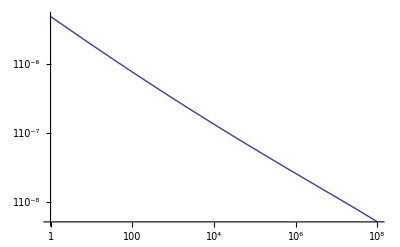

```mathematica
LogLogPlot[Recovery*Starvation/(Starvation+Recovery),{M,1,10^8}]
```